# Taller #4

## Rafael Cepeda

## 1)

u(0,t)=100, U(1,t)=0, f(x)=30sin(πx), L=1m

```mathematica
b[n_]=FourierSinCoefficient[100*(x-1),x,n,FourierParameters->{1,Pi}]
```

-200/(n π)

```mathematica
U[x_,t_,M_]=100(1-x)+30*Sin[Pi*x]*E^(-Pi^(2)*t)-(200/Pi)*Sum[(Sin[n*Pi*x]*E^(-(Pi*n)^(2)*t))/n,{n,M}];
Animate[Plot[U[x,t,30],{x,0,1},PlotRange->{{0,1},{-1,100}}],{t,0,0.07}]
```

u(0,t)=100, U(π,t)=50, f(x)=33x si 0<x≤π/2 y 33(π-x) si π/2<x≤π, L=π m

```mathematica
F[x_]=Piecewise[{{(33*x),0<x≤Pi/2},{33*(Pi-x),Pi/2<x≤Pi}}]
g[x_]=-50*x/Pi+100
```

Piecewise[{{33 x, 0<x≤π/2}, {33 (π-x), π/2<x≤π}, {0, True}}]

100-(50 x)/π

```mathematica
b[n_]=FourierSinCoefficient[F[x]-g[x],x,n,FourierParameters->{1,1}]
```

(4 (25 (-2+(-1)^n) n+33 Sin[(n π)/2]))/(n^2 π)

```mathematica
U[x_,t_,M_]=g[x]+Sum[b[n]*Sin[n*x]*E^(-n^2*t),{n,M}]
```

100-(50 x)/π+∑_n^M (4 ⅇ^(-n^2 t) (25 (-2+(-1)^n) n+33 Sin[(n π)/2]) Sin[n x])/(n^2 π)

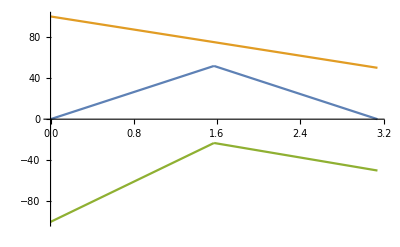

```mathematica
Plot[{F[x],g[x],F[x]-g[x]},{x,0,Pi}]
```

```mathematica
U2[x_,t_,M_]=g[x]+132/Pi*Sum[((-1)^n*E^(-(2*n+1)^2*t)*Sin[(2*n+1)*x])/(2*n+1),{n,0,M}];
```

```mathematica
Animate[Plot[U[x,t,30],{x,0,Pi},PlotRange->{{0,Pi},{-100,100}}],{t,0,0.5}]
```

L=π, f(x)=100x si 0<x≤π/2 y 100(π-x) si π/2<x≤π

```mathematica
F[x_]=Piecewise[{{100*x,0<x≤Pi/2},{100*(Pi-x),Pi/2<x≤Pi}}]
```

Piecewise[{{100 x, 0<x≤π/2}, {100 (π-x), π/2<x≤π}, {0, True}}]

```mathematica
a0=1/Pi*Integrate[F[x],{x,0,Pi}]
```

25 π

```mathematica
a[n_]=FourierCosCoefficient[F[x],x,n,FourierParameters->{1,1}]
```

(800 Cos[(n π)/2] Sin[(n π)/4]^2)/(n^2 π)

```mathematica
U[x_,t_,M_]=a0-(200/Pi)*Sum[(1/((2*k+1)^2))*Cos[2*(2*k+1)*x]*E^(-4(2*k+1)^2*t),{k,0,M}];
```

```mathematica
Animate[Plot[U[x,t,30],{x,0,Pi},PlotRange->{{0,Pi},{0,160}}],{t,0,1.5}]
```

## 3)

```mathematica
Integrate[E^(-x)*(n*Pi*Cos[n*Pi*x]-Sin[n*Pi*x]),{x,0,1}]
```

Sin[n π]/ⅇ

```mathematica
1/Integrate[E^(-x)*E^(-x),{x,0,1}]
```

1/(1/2-1/(2 ⅇ^2))

```mathematica
Integrate[(n*Pi*Cos[n*Pi*x]-Sin[n*Pi*x])*(n*Pi*Cos[n*Pi*x]-Sin[n*Pi*x]),{x,0,1}]
```

1/4 (2 n^2 π^2+2 Cos[2 n π]+(-1/(n π)+n π) Sin[2 n π])

## 6)

```mathematica
coefm[m_]=FourierSinCoefficient[x(Abs[a]-x),x,m,FourierParameters-> {1,Pi/Abs[a]}]
coefn[n_]=FourierSinCoefficient[y(Abs[B]-y),y,n,FourierParameters-> {1,Pi/Abs[B]}]
```

-(4 (-1+(-1)^m) Abs[a]^2)/(m^3 π^3)

-(4 (-1+(-1)^n) Abs[B]^2)/(n^3 π^3)

## 9)

```mathematica
U[X_,y_,t_]=Sin[4*Pi*X]*Sin[Pi*y]*Cos[t];
Animate[Plot3D[{U[x,y,t]},{x,0,1},{y,0,1},PlotRange->{{0,1},{0,1},{-1,1}},Mesh->50],{t,0,Pi,0.00001}]
```

## 10)